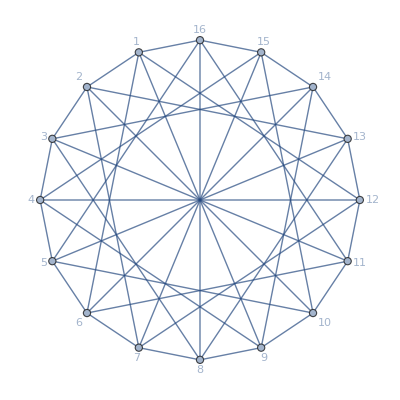

```mathematica
g=CirculantGraph[16,{1,5,8},VertexLabels->"Name"]
```

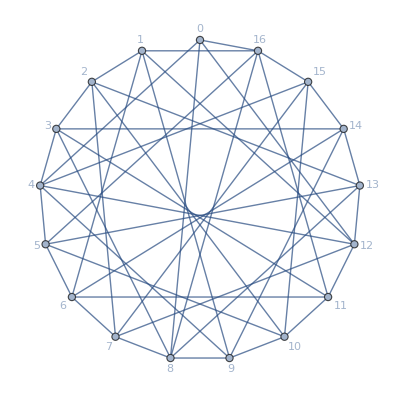

```mathematica
Show[SetProperty[g,VertexLabels->"Name"],PlotRange->All]
```

```mathematica
FindClique[g]
FindIndependentVertexSet[g]
```

{{1,2}}

{{3,6,9,13,15}}

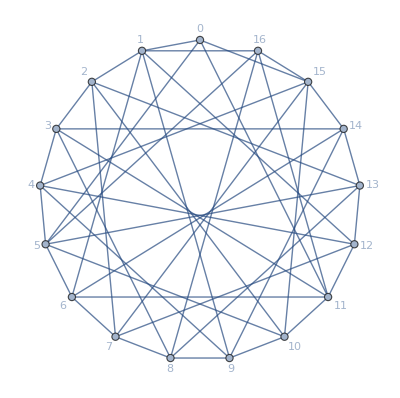

{{1,2}}

{{4,7,10,14,16,0}}

```mathematica
g=VertexAdd[g,0];
g=EdgeAdd[g,{0<->1,0<->15,0<->5,0<->11}];
(*g=EdgeDelete[g,{3<->11,13<->5}];*)
GraphPlot[g,VertexLabels->"Name"]
FindClique[g]
FindIndependentVertexSet[g]
```

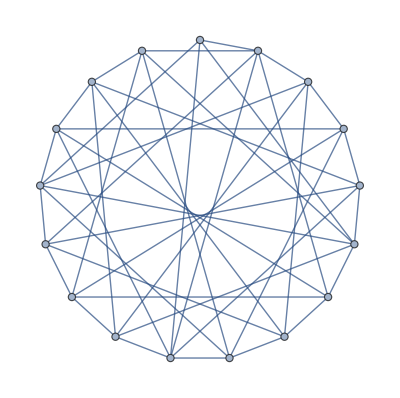

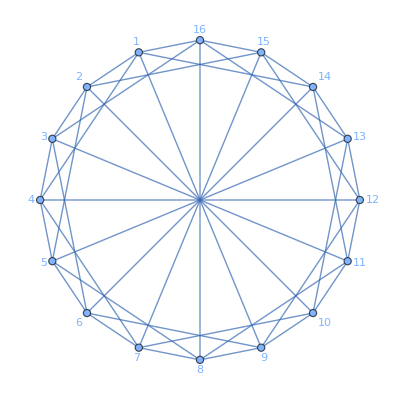

{{1,2}}

{{1,3,5,7,12}}

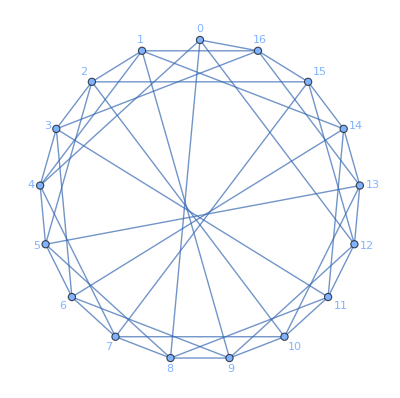

{{1,2}}

{{1,3,5,10,15,0}}

```mathematica
g2=CirculantGraph[16,{1,3,8},VertexLabels->"Name"]
FindClique[g2]
FindIndependentVertexSet[g2]
g2=VertexAdd[g2,0];
g2=EdgeAdd[g2,{0<->4,0<->8,0<->12,0<->16}];
g2=EdgeDelete[g2,{4<->12,8<->16}];
GraphPlot[g2,VertexLabels->"Name"]
FindClique[g2]
FindIndependentVertexSet[g2]
```